# Chapter 6 - Problem 2

## Part I. Functions, Constants, Conversion Factors, and Given Information

Okay so this problem is really similar to the problem earlier. However, we are given a rectangular barrier with a certain width, meaning we are not doing delta approximations like in last game.
PP-PI matrix functions

```mathematica
Clear["Global`*"];
PI[kL_,kR_]= MatrixExp[(1/2) * Log[kL/kR] * ( PauliMatrix[1] - IdentityMatrix[2])];
PP [kx_,l_] = MatrixExp[-I * kx * l * PauliMatrix[3]];
```

Constants and Conversion factors:

```mathematica
h = 6.62607004 * 10^(-34) ;(* planck's constant *)
m = 9.10938 * 10^(-31); (* planck's constant *)
ℏ = h/(2*Pi);
e = 1.60217 * 10 ^(-19); (* 1 electron volt (ev) = e Joules *)
nano = 1 *10^(-9);
```

Given Information and more constants 
IMPORTANT: This is different than the last problem.

```mathematica
V = 1.5;
period = 0.4;
WellWidth = 0.2;
WellDistance = period-WellWidth;

alpha = √((2*m*e)/ℏ^2) * nano; (* the e and nano will help convert everything at once.*)
k = alpha * √epi;
kwell = alpha * √(epi-V);
numofbarriers = 3; (* Keep this the same as in problem 6.1*)
```

## Part II. Transfer Matrix

For this part, we are going to take advantage of the periodicity of a lattice again. By the way, this is a lattice:
-Graphics-Notice how this is periodic, and we can take advantage of this.
Inside we have each period we have the following combination: PI.PP.PI.PP. We must ignore the output “legs” where it is flat during this time. Therefore, we must multiply our end product by PP[k,-WellDistance] as a negation. Also, we will be using 3 barriers rather than 4 shown in the picture I found. Anyway, let’s do it.

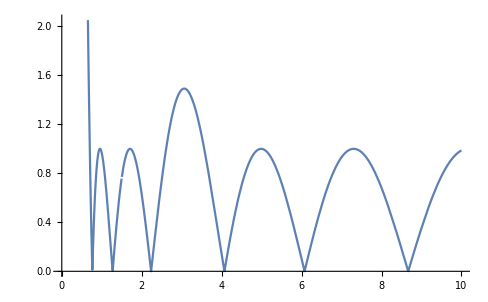

```mathematica
TransferMatrix = PI[k, kwell].PP[kwell,WellWidth].PI[kwell,k].PP[k, WellDistance];
TransferMatrix = MatrixPower[TransferMatrix,numofbarriers](*.PP[k,-WellDistance]*);
Subscript[P, 11]= Tr[TransferMatrix]/2; 
TransferPlot=Plot[Abs[Subscript[P, 11]],{epi,0,10}]
```

Now let’s draw the line at 1, just like last time. We know regions where Re{P_11] <= 1, it is an allowed band. If Re{P_11] > 1, then it is a Forbidden Band.

## Part III. Finding the Forbidden Bands

Following the same steps as in problem 6.1...(if you haven’t read that, please do).

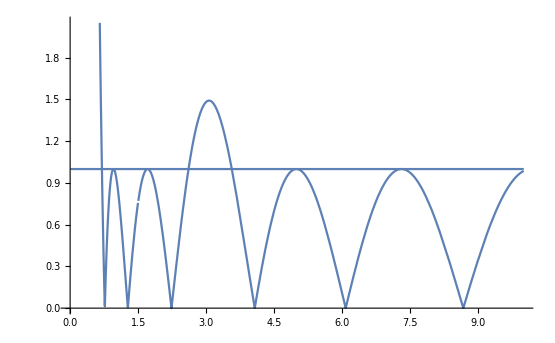

```mathematica
LineAtOne = Plot[1, {epi,0,10}];
Show[TransferPlot, LineAtOne]
```

Another way of seeing when the plot crosses the 1 is by shifting the whole plot down by 1.

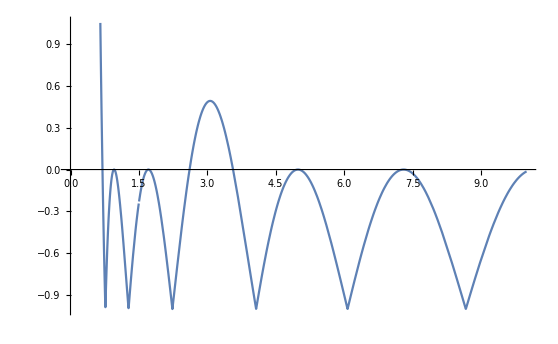

```mathematica
TransferPlot2=Plot[Abs[Subscript[P, 11]] - 1,{epi,0,10}]
```

Whatever you use, make sure you have the proper equality for your FindRoot function. Also another useful thing:
1. RIght click on the graph
2. Click on “Get Coordinates”
3.Then hover your mouse near the root and that’s where you should start your search.
There should be...maybe 8 roots, to make your Arrays and For loop the appropriate size.

```mathematica
(* let's use the for loop method *)
NumOfRoots = 8; (* Number of relavant roots ! *)
Array[ForbiddenRoots, NumOfRoots ]; (* Results *)
Array[StartSearch,NumOfRoots ]; (* where to search *)
StartSearch[1] = 0.9; 
StartSearch[2] = 1.0;
StartSearch[3] = 1.6;
StartSearch[4] = 1.7;
StartSearch[5] =2.5;
StartSearch[6]=3.6;
StartSearch[7] =4.8;
StartSearch[8] =5;
StartSearch[9] =7.2;
StartSearch[10] =7.3;
iterator = 7; (* iterator for the array*)
For[i = 1 , i <=NumOfRoots , i++,
ForbiddenRoots[i]= epi/.FindRoot[Abs[Subscript[P, 11]]== 1,{epi,StartSearch[i]}];]
For[i = 1, i ≤NumOfRoots , i+= 2,
Print["Forbidden band from \n\t", ForbiddenRoots[i], " eV to ", ForbiddenRoots[i+1], " eV"]]
```

Forbidden band from 
	0.956218 eV to 0.956218 eV

Forbidden band from 
	1.70834 eV to 1.70834 eV

Forbidden band from 
	2.6103 eV to 3.56424 eV

Forbidden band from 
	4.98774 eV to 4.98774 eV

Ignoring the singular values when Abs[P11] == 1, we only have one forbidden band from 2.6103 eV to 3.56424 eV